```mathematica
SetDirectory[NotebookDirectory[]];
<<X`
```

## Data (e^+e^-→ γ + inv.)

```mathematica
BelleII20fbINV=ImportString["0.000101324  0.000064858
0.000810161  0.000064858
0.004979008  0.000064858
0.016271537  0.000064858
0.028276690  0.000065888
0.033113112  0.000066933
0.038776752  0.000070170
0.045409096  0.000077122
0.049139255  0.000088862
0.049139255  0.000140284
0.047237370  0.000169457
0.044815534  0.000204697
0.038269884  0.000338777
0.027907073  0.000792767
0.019562690  0.001769552
0.014265458  0.003708777
0.009612960  0.008816560
0.007009940  0.017350670
0.005317583  0.033612106
0.004087225  0.059244709
0.003444632  0.086447440","Table"]//Flatten;
```

```mathematica
BelleII50abINV=ImportString["0.000100429 0.000008981
0.001974872 0.000008981
0.017518399 0.000008981
0.052850406 0.000008981
0.090625219 0.000009261
0.108471585 0.000009848
0.120205863 0.000010798
0.129832345 0.000012209
0.133209536 0.000014234
0.133209536 0.000017113
0.129832345 0.000020575
0.120205863 0.000027123
0.111293141 0.000035755
0.097882785 0.000050119
0.070101112 0.000122086
0.048307534 0.000297395
0.025097372 0.001298175
0.012872575 0.005495409
0.007506970 0.017646829
0.004977669 0.042986623
0.003850365 0.074702190
0.003300558 0.101546899","Table"]//Flatten;
```

## Data (e^+e^-→ 3γ)

```mathematica
BelleII20fb3γ =ImportString["0.147619925 0.001015469
0.129832345 0.001513561
0.112731325 0.002550743
0.099147673 0.004168694
0.082835331 0.007943282
0.159441815 0.000770312
0.172210441 0.000566674
0.186001621 0.000443268
0.200897243 0.000368695
0.222629978 0.000316228
0.253131227 0.000284010
0.295297808 0.000288403
0.327242641 0.000288403
0.367329461 0.000292864
0.401873361 0.000311411
0.451102354 0.000321119
0.506361837 0.000331131
0.568390539 0.000341455
0.671641536 0.000357547
0.763659270 0.000368695
0.890869573 0.000380189
1.012922477 0.000392043
1.181655025 0.000416869
1.378495029 0.000436516
1.649955073 0.000471339
1.924804464 0.000501187
2.303846457 0.000532926
2.687621024 0.000566674
3.135324729 0.000602560
3.657606883 0.000660693
4.266890759 0.000713400
5.107147944 0.000819093
5.881887702 0.000926119
6.602411708 0.001063327
7.316649782 0.001258925
7.902591204 0.001513561
8.319061779 0.001847850
8.645755985 0.002326305
8.985279655 0.002884032
9.219004243 0.003801894
9.338136610 0.004860340","Table"];
```

```mathematica
BelleII50ab3γ = ImportString["0.159441815 0.000111344
0.163589207 0.000095499
0.172210441 0.000081909
0.176689970 0.000070253
0.186001621 0.000062135
0.195804001 0.000054954
0.211484630 0.000047134
0.234362691 0.000041687
0.273402810 0.000040427
0.310860153 0.000041052
0.353449309 0.000041687
0.412326868 0.000044327
0.456931713 0.000045709
0.512905286 0.000046416
0.575735552 0.000047863
0.689112238 0.000050119
0.846270678 0.000053293
1.012922477 0.000055804
1.243928846 0.000059338
1.608124626 0.000065063
2.303846457 0.000074702
3.135324729 0.000087096
3.850364626 0.000095499
4.549802710 0.000104713
5.376297237 0.000120226
6.271880421 0.000142342
7.131154591 0.000171133
7.902591204 0.000212162
8.319061779 0.000263027
8.645755985 0.000326087
8.870648902 0.000392043
9.101391722 0.000486034
9.338136610 0.000584341
9.458808462 0.000747022","Table"];
```

## Loop functions

```mathematica
f[x_]:= Piecewise[{{ArcSin[1/(√x)],x≥1},{π/2+ⅈ/2 Log[(1+√(1-x))/(1-√(1-x))],x<1}}]
```

```mathematica
B3[x_,y_]:= 1-(x*y)/(y-x)(f[x]^2-f[y]^2)
```

```mathematica
B3CPVren[m_,mϕ_,s_]:=(m (Log[(2 m^2-mϕ^2+√(-4 m^2 mϕ^2+mϕ^4))/(2 m^2)]^2-Log[(2 m^2-s+√(s (-4 m^2+s)))/(2 m^2)]^2))/(mϕ^2-s)
```

```mathematica
B3CPCren[m_,mϕ_,s_]:=-1/(2(mϕ^2-s)^2)  m (4 mϕ^2-4 s+4 s DiscB[mϕ^2,m,m]-4 s DiscB[s,m,m]+4 m^2 Log[(2 m^2-mϕ^2+√(-4 m^2 mϕ^2+mϕ^4))/(2 m^2)]^2-mϕ^2 Log[(2 m^2-mϕ^2+√(-4 m^2 mϕ^2+mϕ^4))/(2 m^2)]^2+s Log[(2 m^2-mϕ^2+√(-4 m^2 mϕ^2+mϕ^4))/(2 m^2)]^2-4 m^2 Log[(2 m^2-s+√(s (-4 m^2+s)))/(2 m^2)]^2+mϕ^2 Log[(2 m^2-s+√(s (-4 m^2+s)))/(2 m^2)]^2-s Log[(2 m^2-s+√(s (-4 m^2+s)))/(2 m^2)]^2)
```

## ALP (PS+anomaly)

Limits are on (|cτ|)/fa*mτ.

### e^+e^-→ γ + inv.

```mathematica
BelleII20fbINVRecastALP=Table[{BelleII20fbINV[[2i-1]],(π(BelleII20fbINV[[2i]]*mTA))/(αEM*Abs[B3[(4 mTA^2)/BelleII20fbINV[[2i-1]]^2,(4 mTA^2)/s]]) /. {αEM->1/137,mTA->1.777,s-> 10.58^2}},{i,1,Length[BelleII20fbINV]/2}];
```

```mathematica
BelleII50abINVRecastALP=Table[{BelleII50abINV[[2i-1]],(π(BelleII50abINV[[2i]]*mTA))/(αEM*Abs[B3[(4 mTA^2)/BelleII50abINV[[2i-1]]^2,(4 mTA^2)/s]]) /. {αEM->1/137,mTA->1.777,s-> 10.58^2}},{i,1,Length[BelleII20fbINV]/2}];
```

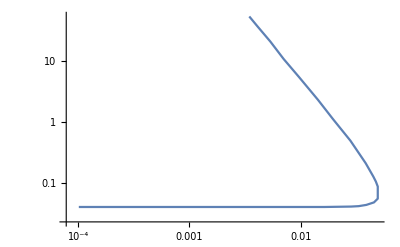

```mathematica
ListLogLogPlot[BelleII20fbINVRecastALP,Joined->True,PlotRange->All]
```

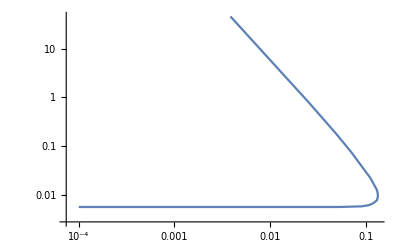

```mathematica
ListLogLogPlot[BelleII50abINVRecastALP,Joined->True,PlotRange->All]
```

```mathematica
SuperPlus[e] SuperMinus[e]-> 3γ
```

```mathematica
BelleII20fb3γRecastALP=Table[{BelleII20fb3γ[[i,1]],(π(BelleII20fb3γ[[i,2]]*mTA))/(αEM*Abs[B3[(4 mTA^2)/BelleII20fb3γ[[i,1]]^2,(4 mTA^2)/s]]) /. {αEM->1/137,mTA->1.777,s-> 10.58^2}},{i,1,Length[BelleII20fb3γ]}];
```

```mathematica
BelleII50ab3γRecastALP=Table[{BelleII50ab3γ[[i,1]],(π(BelleII50ab3γ[[i,2]]*mTA))/(αEM*Abs[B3[(4 mTA^2)/BelleII50ab3γ[[i,1]]^2,(4 mTA^2)/s]]) /. {αEM->1/137,mTA->1.777,s-> 10.58^2}},{i,1,Length[BelleII50ab3γ]}];
```

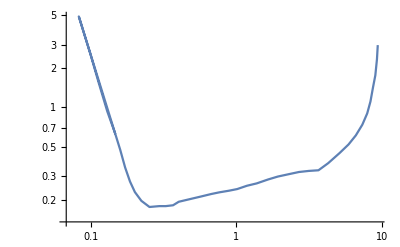

```mathematica
ListLogLogPlot[BelleII20fb3γRecastALP,Joined->True,PlotRange->All]
```

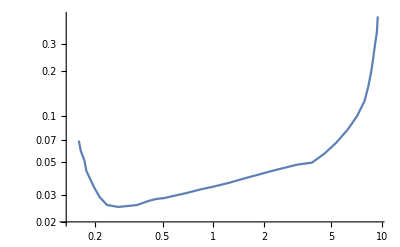

```mathematica
ListLogLogPlot[BelleII50ab3γRecastALP,Joined->True,PlotRange->All]
```

## Pseudoscalar (without anomaly)

Limits are on g_τ^PS.

```mathematica
SuperPlus[e] SuperMinus[e]-> γ + inv.
```

```mathematica
BelleII20fbINVRecastPS=Table[{BelleII20fbINV[[2i-1]],(π(BelleII20fbINV[[2i]]*mTA))/(αEM*Abs[-1+B3[(4 mTA^2)/BelleII20fbINV[[2i-1]]^2,(4 mTA^2)/s]]) /. {αEM->1/137,mTA->1.777,s-> 10.58^2}},{i,1,Length[BelleII20fbINV]/2}];
```

```mathematica
BelleII50abINVRecastPS=Table[{BelleII50abINV[[2i-1]],(π(BelleII50abINV[[2i]]*mTA))/(αEM*Abs[-1+B3[(4 mTA^2)/BelleII50abINV[[2i-1]]^2,(4 mTA^2)/s]]) /. {αEM->1/137,mTA->1.777,s-> 10.58^2}},{i,1,Length[BelleII20fbINV]/2}];
```

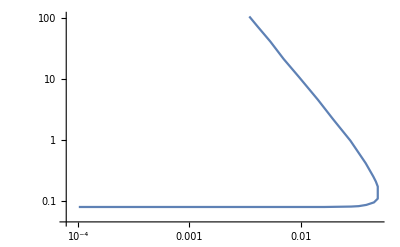

```mathematica
ListLogLogPlot[BelleII20fbINVRecastPS,Joined->True,PlotRange->All]
```

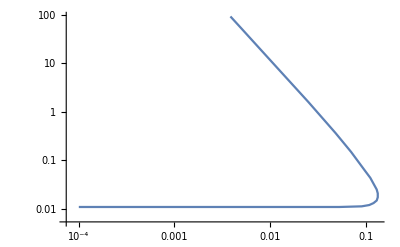

```mathematica
ListLogLogPlot[BelleII50abINVRecastPS,Joined->True,PlotRange->All]
```

```mathematica
SuperPlus[e] SuperMinus[e]-> 3γ
```

```mathematica
BelleII20fb3γRecastPS=Table[{BelleII20fb3γ[[i,1]],(π(BelleII20fb3γ[[i,2]]*mTA))/(αEM*Abs[-1+B3[(4 mTA^2)/BelleII20fb3γ[[i,1]]^2,(4 mTA^2)/s]]) /. {αEM->1/137,mTA->1.777,s-> 10.58^2}},{i,1,Length[BelleII20fb3γ]}];
```

```mathematica
BelleII50ab3γRecastPS=Table[{BelleII50ab3γ[[i,1]],(π(BelleII50ab3γ[[i,2]]*mTA))/(αEM*Abs[-1+B3[(4 mTA^2)/BelleII50ab3γ[[i,1]]^2,(4 mTA^2)/s]]) /. {αEM->1/137,mTA->1.777,s-> 10.58^2}},{i,1,Length[BelleII50ab3γ]}];
```

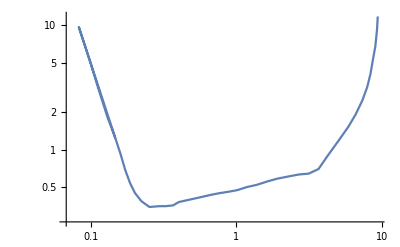

```mathematica
ListLogLogPlot[BelleII20fb3γRecastPS,Joined->True,PlotRange->All]
```

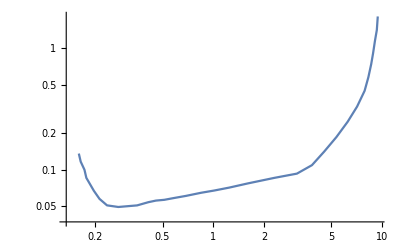

```mathematica
ListLogLogPlot[BelleII50ab3γRecastPS,Joined->True,PlotRange->All]
```

## Scalar (CP even)

Limits are on g_τ^S.

### e^+e^-→ γ + inv.

```mathematica
BelleII20fbINVRecastS=Table[{BelleII20fbINVRecastPS[[i,1]],√(2/3) Abs[B3CPVren[mTA,BelleII20fbINVRecastPS[[i,1]],s]]/Abs[B3CPCren[mTA,BelleII20fbINVRecastPS[[i,1]],s]] BelleII20fbINVRecastPS[[i,2]]/. {αEM->1/137,mTA->1.777,s-> 10.58^2}},{i,1,Length[BelleII20fbINVRecastPS]}];
```

```mathematica
BelleII50abINVRecastS=Table[{BelleII50abINVRecastPS[[i,1]],√(2/3) Abs[B3CPVren[mTA,BelleII50abINVRecastPS[[i,1]],s]]/Abs[B3CPCren[mTA,BelleII50abINVRecastPS[[i,1]],s]] BelleII50abINVRecastPS[[i,2]]/. {αEM->1/137,mTA->1.777,s-> 10.58^2}},{i,1,Length[BelleII50abINVRecastPS]}];
```

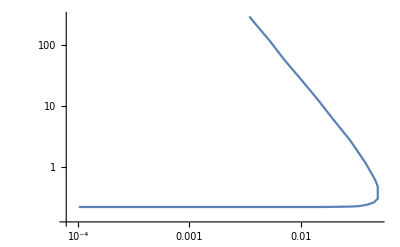

```mathematica
ListLogLogPlot[BelleII20fbINVRecastS,Joined->True,PlotRange->All]
```

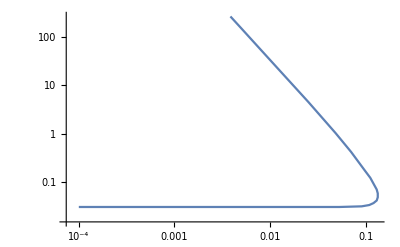

```mathematica
ListLogLogPlot[BelleII50abINVRecastS,Joined->True,PlotRange->All]
```

```mathematica
SuperPlus[e] SuperMinus[e]-> 3γ
```

```mathematica
BelleII20fb3γRecastS=Table[{BelleII20fb3γRecastPS[[i,1]],√(2/3) Abs[B3CPVren[mTA,BelleII20fb3γRecastPS[[i,1]],s]]/Abs[B3CPCren[mTA,BelleII20fb3γRecastPS[[i,1]],s]] BelleII20fb3γRecastPS[[i,2]]/. {αEM->1/137,mTA->1.777,s-> 10.58^2}},{i,1,Length[BelleII20fb3γRecastPS]}];
```

```mathematica
BelleII50ab3γRecastS=Table[{BelleII50ab3γRecastPS[[i,1]],√(2/3) Abs[B3CPVren[mTA,BelleII50ab3γRecastPS[[i,1]],s]]/Abs[B3CPCren[mTA,BelleII50ab3γRecastPS[[i,1]],s]] BelleII50ab3γRecastPS[[i,2]]/. {αEM->1/137,mTA->1.777,s-> 10.58^2}},{i,1,Length[BelleII50ab3γRecastPS]}];
```

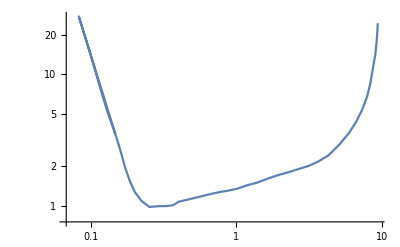

```mathematica
ListLogLogPlot[BelleII20fb3γRecastS,Joined->True,PlotRange->All]
```

```mathematica
ListLogLogPlot[BelleII20fb3γRecastS,Joined->True,PlotRange->All]
```

-Graphics-

## Plots

### e^+e^-→ γ + inv.

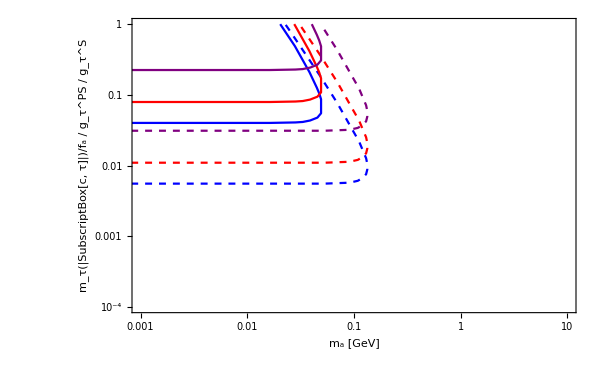

```mathematica
Show[ListLogLogPlot[BelleII20fbINVRecastALP,Joined->True,PlotRange->{{0.001,10},{0.1/1000,1}},PlotStyle->{Blue},Frame->True,FrameStyle->Directive[FontSize->15, FontFamily-> "Times New Roman",Black],FrameLabel->{Style["m_a [GeV]", FontSize->15,FontFamily->"Times New Roman",Black],Style["m_τ(|SubscriptBox[c, τ]|)/f_a / g_τ^PS / g_τ^S", FontSize->15,FontFamily->"Times New Roman",Black]},ImageSize->600],ListLogLogPlot[BelleII50abINVRecastALP,Joined->True,PlotRange->{{0.001,10},{0.1/1000,1}},PlotStyle->{Dashed, Blue}],
ListLogLogPlot[BelleII20fbINVRecastPS,Joined->True,PlotRange->{{0.001,10},{0.1/1000,1}},PlotStyle->{Red}],
ListLogLogPlot[BelleII50abINVRecastPS,Joined->True,PlotRange->{{0.001,10},{0.1/1000,1}},PlotStyle->{Dashed, Red}],
ListLogLogPlot[BelleII20fbINVRecastS,Joined->True,PlotRange->{{0.001,10},{0.1/1000,1}},PlotStyle->{Purple}],
ListLogLogPlot[BelleII50abINVRecastS,Joined->True,PlotRange->{{0.001,10},{0.1/1000,1}},PlotStyle->{Dashed, Purple}]]
```

```mathematica
SuperPlus[e] SuperMinus[e]-> 3γ
```

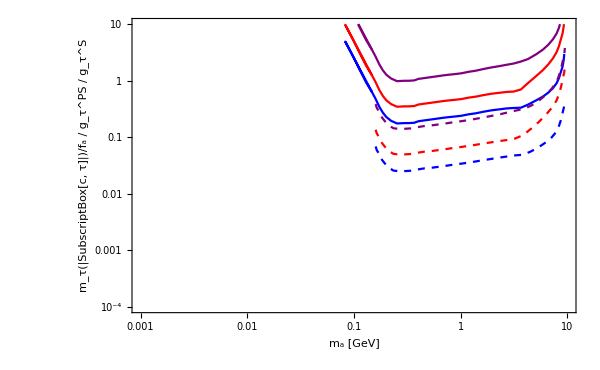

```mathematica
Show[ListLogLogPlot[BelleII20fb3γRecastALP,Joined->True,PlotRange->{{0.001,10},{0.1/1000,10}},PlotStyle->{Blue},Frame->True,FrameStyle->Directive[FontSize->15, FontFamily-> "Times New Roman",Black],FrameLabel->{Style["m_a [GeV]", FontSize->15,FontFamily->"Times New Roman",Black],Style["m_τ(|SubscriptBox[c, τ]|)/f_a / g_τ^PS / g_τ^S", FontSize->15,FontFamily->"Times New Roman",Black]},ImageSize->600],ListLogLogPlot[BelleII50ab3γRecastALP,Joined->True,PlotRange->{{0.001,10},{0.1/1000,10}},PlotStyle->{Dashed, Blue}],
ListLogLogPlot[BelleII20fb3γRecastPS,Joined->True,PlotRange->{{0.001,10},{0.1/1000,10}},PlotStyle->{Red}],
ListLogLogPlot[BelleII50ab3γRecastPS,Joined->True,PlotRange->{{0.001,10},{0.1/1000,10}},PlotStyle->{Dashed, Red}],
ListLogLogPlot[BelleII20fb3γRecastS,Joined->True,PlotRange->{{0.001,10},{0.1/1000,10}},PlotStyle->{Purple}],
ListLogLogPlot[BelleII50ab3γRecastS,Joined->True,PlotRange->{{0.001,10},{0.1/1000,10}},PlotStyle->{Dashed, Purple}]]
```

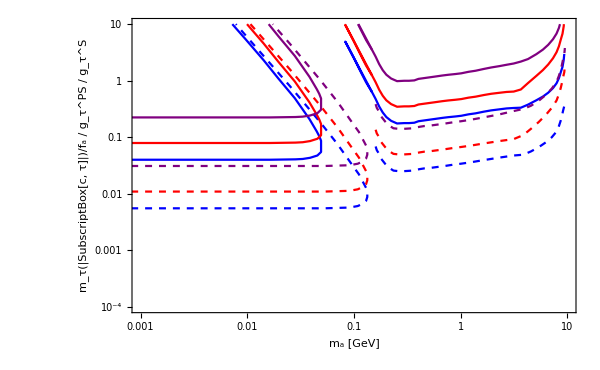

```mathematica
Show[ListLogLogPlot[BelleII20fbINVRecastALP,Joined->True,PlotRange->{{0.001,10},{0.1/1000,10}},PlotStyle->{Blue},Frame->True,FrameStyle->Directive[FontSize->15, FontFamily-> "Times New Roman",Black],FrameLabel->{Style["m_a [GeV]", FontSize->15,FontFamily->"Times New Roman",Black],Style["m_τ(|SubscriptBox[c, τ]|)/f_a / g_τ^PS / g_τ^S", FontSize->15,FontFamily->"Times New Roman",Black]},ImageSize->600],ListLogLogPlot[BelleII50abINVRecastALP,Joined->True,PlotRange->{{0.001,10},{0.1/1000,10}},PlotStyle->{Dashed, Blue}],
ListLogLogPlot[BelleII20fbINVRecastPS,Joined->True,PlotRange->{{0.001,10},{0.1/1000,10}},PlotStyle->{Red}],
ListLogLogPlot[BelleII50abINVRecastPS,Joined->True,PlotRange->{{0.001,10},{0.1/1000,10}},PlotStyle->{Dashed, Red}],
ListLogLogPlot[BelleII20fbINVRecastS,Joined->True,PlotRange->{{0.001,10},{0.1/1000,10}},PlotStyle->{Purple}],
ListLogLogPlot[BelleII50abINVRecastS,Joined->True,PlotRange->{{0.001,10},{0.1/1000,10}},PlotStyle->{Dashed, Purple}],ListLogLogPlot[BelleII20fb3γRecastALP,Joined->True,PlotRange->{{0.001,10},{0.1/1000,10}},PlotStyle->{Blue},Frame->True,FrameStyle->Directive[FontSize->15, FontFamily-> "Times New Roman",Black],FrameLabel->{Style["m_a [GeV]", FontSize->15,FontFamily->"Times New Roman",Black],Style["m_τ(|SubscriptBox[c, τ]|)/f_a / g_τ^PS / g_τ^S", FontSize->15,FontFamily->"Times New Roman",Black]},ImageSize->600],ListLogLogPlot[BelleII50ab3γRecastALP,Joined->True,PlotRange->{{0.001,10},{0.1/1000,10}},PlotStyle->{Dashed, Blue}],
ListLogLogPlot[BelleII20fb3γRecastPS,Joined->True,PlotRange->{{0.001,10},{0.1/1000,10}},PlotStyle->{Red}],
ListLogLogPlot[BelleII50ab3γRecastPS,Joined->True,PlotRange->{{0.001,10},{0.1/1000,10}},PlotStyle->{Dashed, Red}],
ListLogLogPlot[BelleII20fb3γRecastS,Joined->True,PlotRange->{{0.001,10},{0.1/1000,10}},PlotStyle->{Purple}],
ListLogLogPlot[BelleII50ab3γRecastS,Joined->True,PlotRange->{{0.001,10},{0.1/1000,10}},PlotStyle->{Dashed, Purple}]]
```